# Ink Bottle Example C.T. Miller 20 August 2018

## Introduction

The purpose of this notebook is to document an ink bottle example, which is traditionally used to explain the origin of capillary pressure hysteresis in porous medium systems.  We will describe an analytical geometry of the system, compute the equilibrium states from a set of constant pressure boundary conditions for both drainage and imibibition, and we will then compute the Minkowski functionals corresponding to this example to demonstrate that for a state equation formulated in agreement with Hadwiger’s theorem and Steiner’s formula, the resulting description is hysteretic free. We will choose a simple geometry, a zero contact angle, the wetting reservoir at the origin, or left-hand side of the domain, and the non-wetting reservoir on the terminus of the domain, or the right-hand side.

## Geometric Definitions

First, describe the geometry of the analytical ink bottle and visualize the system.

```mathematica
y[m_,n_,p_,q_,t_, x_]:= m Cos [n x]+ p Sin[q x] + t
```

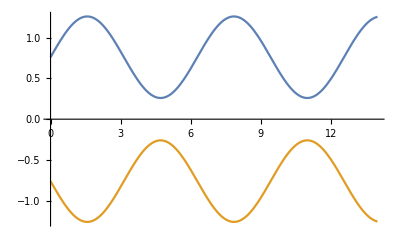

```mathematica
Plot[{y[0.01, 0.01, 0.5, 1.0, 0.75, x],-y[0.01, 0.01, 0.5, 1.0, 0.75, x]},{x,0,14}]
```

Define a function to compute the volume of the ink bottle between limits. This will be used along with a correction for the interface to compute saturations.

```mathematica
volume[m_,n_,p_,q_,t_, x1_, x2_]:=  Pi Integrate[y[m,n,p,q,t,x]^2,{x,x1,x2}]
```

```mathematica
volume[0.01,0.01,0.5,1.,0.75,0.,14.]
```

32.9077

We will also need the slope of the ink bottle, which can be computed analytically as well. This slope will be used to determine the capillary pressure and hence interface shape at locations in x along the domain.

```mathematica
D[m Cos [n x]+ p Sin[q x] + t,x]
```

p q Cos[q x]-m n Sin[n x]

```mathematica
dydx[m_,n_,p_,q_, x_]:= p q Cos [q x]- m n Sin[n x]
```

We will be constructing spherical caps in two-dimensions, which are portions of a circle. The radius of the circle will relate to the capillary pressure through Laplace’s law. Let’s introduce a parametric plot of a portion of a circle, which will be used to plot a series of interfaces in the ink bottle. The convention with this parameterization is counterclockwise starting from the positive x axis.

```mathematica
Interface[xc_,yc_,r_,t1_,t2_]:=ParametricPlot[{xc+r Cos[t],yc+r Sin[t]},{t,t1,t2}]
```



```mathematica
Interface[0,0,1,0,2 Pi]
```

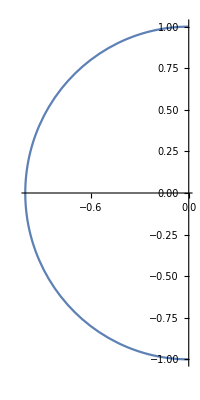

```mathematica
Interface[0,0,1,Pi/2,3 Pi/2]
```

## Capillary Pressure-Saturation Relation

In this section, we will compute and visualize equilibrium interfaces corresponding to a set of positions in the x direction of the common curve. These equilibrium interface conditions will in turn be used to compute the capillary pressures and saturations that correspond to these states.  This solution is based upon Laplace’s equation for an interface and assumes a spherical cap.  We will assume the example geometry shown in the geometry section, but formulate the solution generally, except we will assume a zero contact angle.  We will need to compute the derivative dy/dx and use the equation for the tangent slope on a circle, the equation for a circle, and knowledge that the center of the circle has yc=0 to compute the radius of the circle and the xc location of the centroid. The value of dy/dx comes from the geometry of the ink bottle, which we have analytically defined in the geometry section. 

We will start with an example computation to find the location and radius of the sphere given an x location for the interface and the slope corresponding to the end of our domai, which is x=14.

```mathematica
dydx[0.01,0.01,0.5,1.0, 14]
```

0.0683547

```mathematica
Solve[dydx[0.01,0.01,0.5,1.0, 14]==-(14.-xc)/ y[0.01,0.01, 0.5,1.0,0.75,14] && (14.-xc)^2 + y[0.01,0.01, 0.5,1.0,0.75,14.]^2==r^2 && r>0, {xc, r}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xc→14.0858,r→1.25813}}

A function can be introduced to find the location and radius of the spherical cap for a given interface location.

```mathematica
solveInterface[m_,n_,p_,q_, t_,xi_,xf_,xint_]:=Solve[dydx[m,n, p,q,xint]==-(xint-xc)/ y[m,n,p,q,t,xint] && (xint-xc)^2 + y[m,n,p,q,t,xint]^2==r^2 && r>0, {xc, r}]
```

```mathematica
solveInterface[0.01,0.01,0.5,1.,0.75,0.,14.,14.]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xc→14.0858,r→1.25813}}

```mathematica
solveInterface[0.01,0.01,0.5,1.,0.75,0.,14.,13.9]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xc→14.0463,r→1.25447}}

Use the parametric equation for a circle to determine the interface parametric domain and plot the interface.

```mathematica
ArcCos[(14.-14.0858)/1.25813]
```

1.63905

```mathematica
%-Pi/2.
```

0.0682494

```mathematica
3Pi/2-%
```

4.64414

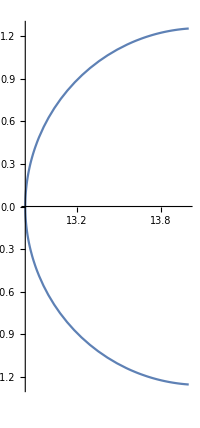

```mathematica
Interface[14.0858,0,1.25813,1.63905,4.64414]
```

We can write a function to visualize the interface more conveniently.

```mathematica
Vint[x_,xc_,yc_,r_]:=Interface[xc,yc,r,ArcCos[(x-xc)/r],2Pi-ArcCos[(x-xc)/r]]
```

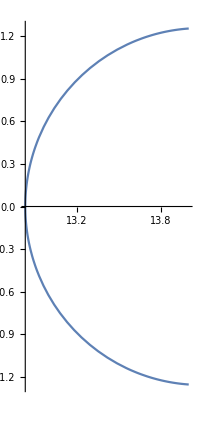

```mathematica
Vint[14.,14.0858,0.,1.25813]
```

It would be useful to know where the ink bottle radius is increasing and decreasing to guide the selection of the set of equilibrium points that we wish to evaluate.

```mathematica
Solve[D[dydx[0.01,0.01,0.5,1.0, x]]==0&& x >0 &&x<14,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1.57079},{x→4.7124},{x→7.85397},{x→10.9956}}

What we would like is to specify a set of points within the domain, which could track drainage and imbibition, and to compute the corresponding centroid of the circles, the radius of the circles, the capillary pressures, and the saturations that correspond to the set of interface locations. The capillary pressure is computed from Laplace’s equation by the following function. By specifying an interface location, r will be computed, which can in turn be used to compute the corresponding capillary pressure.

```mathematica
pc[r_,ift_]:=2. ift/r
```

```mathematica
pc[1.25813,1.]
```

1.58966

To compute the saturation we need to compute the volume of the ink bottle, what was previously defined, and the volume of the non-wetting phase, which can be computed from knowing the location and shape of the interface. The volume of the spherical  is determined readily from the available equation, and it is implemented in a function.consisting of the width of the ink bottle and the distance to the center of the circle.

```mathematica
cap[x_,xc_,r_]:=(Pi(r-xc+x)^2(3 r-(r- xc+x)))/3.
```

```mathematica
cap[14.,14.0858,1.25813]
```

3.74495

```mathematica
sw[m_,n_,p_,q_,t_,xi_,xf_,xint_,xc_,r_]:=(volume[m,n,p,q,t, xi, xint]-cap[xint,xc,r])/volume[m,n,p,q,t, xi, xf]
```

```mathematica
sw[0.01,0.01,0.5,1.,0.75,0.,14.,14.,14.0858,1.25813]
```

0.886199

Let’s use a rule replacement to solve for sw using the previously defined function to supply the rule and extract the solution, which is returned as a list because of the application of list of rules from the interface solution. This can be written to return to return a list with the state sw, pc, r, xc, which is all the information needed at a given location to determine the capillary pressure saturation relation and plot the interface..

```mathematica
{sw[0.01,0.01,0.5,1.,0.75,0.,14.,14.,xc,r],pc[r,1.],r,xc}/.solveInterface[0.01,0.01,0.5,1.,0.75,0.,14.,14.]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.886197,1.58965,1.25813,14.0858}}

Let’s define a state function to return the {sw,pc,r,xint,xc} state of the system from a set of inputs.

```mathematica
state[m_,n_,p_,q_,t_,xi_,xf_,xint_]:=({sw[m,n,p,q,t,xi,xf,xint,xc,r],pc[r,1.],r,xint,xc}/.solveInterface[m,n,p,q,t,xi,xf,xint])[[1]]
```

```mathematica
state[0.01,0.01,0.5,1.,0.75,0.,14.,14.]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.886197,1.58965,1.25813,14.,14.0858}

## Capillary Pressure Saturation Example

We can use the definition defined above to solve an example problem in detail. We will use a system consistent with the example worked above to show the functions used in this approach. The goal now is to construct a complete drainage and imbibition curve for the ink bottle. 

Physically the situation is that the location of interface at any location along the curve must have an interface shape that matches the geometry of the system and obeys Laplace’s law.  If one were to control sw all locations of the interface would be accessible.  Alternatively, one can pick a set, or list, of interface locations and compute the corresponding state that correspondes to these locations.  Because the geometry of the ink bottle changes, for a monotonic set of  locations in x of the interface the capillary pressure will not be monotonic.  The traditional way of representing the ink bottle is to examine the state under monotonically increasing capillary pressure starting from fully water saturated conditions to evaluate drainage, and to examine the state under monotonically decreasing capillary pressure starting from a non-wetting phase saturated state for the imbibition case.  For drainage, the sequence of states will move the interface from the non-wetting boundary toward the wetting phase boundary. For imbibition, the sequence of states will move the fluid-fluid interface from the wetting-phase boundary toward the non-wetting-phase boundary. Because of the geometry of the system, the equilibrium states will differ for drainage and imbibition, which is the classical example used to claim pc-sw relations are inherently hysteretic. 

First, we will create a list of locations along the domain. We have previously located the extrema of this geometry. We can then compute a regular list of locations and add to this list the locations of the extrema so that all interesting features of the solution are captured.

```mathematica
xreg=Table[i,{i,0,14,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.}

```mathematica
Solve[D[dydx[0.01,0.01,0.5,1.0, x]]==0&& x >0 &&x<14,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1.57079},{x→4.7124},{x→7.85397},{x→10.9956}}

```mathematica
extrema=x/.%
```

{1.57079,4.7124,7.85397,10.9956}

```mathematica
xset=Sort[Join[xreg,extrema]]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.57079,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.7124,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.85397,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,10.9956,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.}

```mathematica
Length[xset]
```

145

All of the states near the wetting phase boundary may not be physical, since once the interface exits the domain, we will have saturated conditions. So screen the conditions to figure out which entries should be trimmed from xset.

```mathematica
state[0.01,0.01,0.5,1.,0.75,0.,14.,xset[[9]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.0142243,1.68832,1.18461,0.8,1.18969}

Now compute the set of states that correspond to the set of interface locations of interest within the domain. This list can then be manipulated to extract subsets that correspond to portions of the state space of interest---for example drainage and imbibition for the standard ink bottle example corresponding to monotonic changes in capillary pressure. We start the set away from the boundary to avoid negative saturations corresponding to the interface leaving the domain.

```mathematica
stateSet=Table[state[0.01,0.01,0.5,1.,0.75,0.,14.,xset[[i]]],{i,9,145}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{0.0142243,1.68832,1.18461,0.8,1.18969},{0.0186149,1.65837,1.20601,0.9,1.25794},{0.0230807,1.63524,1.22306,1.,1.31898},{0.0276041,1.61783,1.23622,1.1,1.37343},{0.0321861,1.60516,1.24598,1.2,1.42213},{0.0368555,1.59638,1.25284,1.3,1.46609},{0.0416772,1.59079,1.25724,1.4,1.50646},{0.0467606,1.58789,1.25953,1.5,1.54452},{0.0506026,1.5873,1.26,1.57079,1.57079},{0.0522653,1.5874,1.25992,1.6,1.58161},{0.058401,1.58928,1.25843,1.7,1.61909},{0.0654213,1.5937,1.25494,1.8,1.65835},{0.0736081,1.60108,1.24916,1.9,1.70067},{0.0832473,1.61204,1.24066,2.,1.74726},{0.094596,1.62737,1.22898,2.1,1.79921},{0.107846,1.64799,1.2136,2.2,1.85742},{0.123086,1.67496,1.19406,2.3,1.9226},{0.140276,1.70945,1.16996,2.4,1.99527},{0.159227,1.75276,1.14105,2.5,2.0757},{0.179604,1.80632,1.10723,2.6,2.16395},{0.200948,1.8717,1.06855,2.7,2.25986},{0.222708,1.95072,1.02526,2.8,2.36305},{0.244291,2.04541,0.977801,2.9,2.47296},{0.265121,2.1581,0.926739,3.,2.58888},{0.28468,2.29149,0.872795,3.1,2.70994},{0.302559,2.44861,0.816791,3.2,2.83522},{0.318476,2.63289,0.759621,3.3,2.9637},{0.332289,2.84812,0.702218,3.4,3.09438},{0.343985,3.09831,0.645513,3.5,3.22627},{0.353663,3.38748,0.59041,3.6,3.35844},{0.361504,3.71921,0.537749,3.7,3.49006},{0.367739,4.09597,0.488284,3.8,3.62042},{0.37262,4.51802,0.442672,3.9,3.74896},{0.3764,4.9819,0.401454,4.,3.87529},{0.379307,5.47859,0.365057,4.1,3.99916},{0.381543,5.99158,0.333802,4.2,4.12053},{0.383275,6.49539,0.307911,4.3,4.2395},{0.384636,6.95591,0.287525,4.4,4.35633},{0.385732,7.33333,0.272727,4.5,4.47141},{0.386642,7.58848,0.263557,4.6,4.58524},{0.387426,7.69135,0.260032,4.7,4.69839},{0.387517,7.69264,0.259989,4.7124,4.7124},{0.388132,7.62903,0.262157,4.8,4.81146},{0.388796,7.40939,0.269928,4.9,4.92506},{0.389447,7.05884,0.283333,5.,5.03979},{0.390112,6.61511,0.302338,5.1,5.15614},{0.390813,6.11855,0.326875,5.2,5.27455},{0.391572,5.60512,0.356817,5.3,5.39531},{0.392413,5.10251,0.391964,5.4,5.51856},{0.393357,4.6294,0.432022,5.5,5.64429},{0.394427,4.19648,0.47659,5.6,5.77231},{0.395646,3.8084,0.525155,5.7,5.90227},{0.397038,3.46566,0.57709,5.8,6.03363},{0.398623,3.16625,0.631662,5.9,6.16574},{0.400424,2.90676,0.688051,6.,6.29778},{0.402459,2.68325,0.745366,6.1,6.42885},{0.404744,2.49166,0.802679,6.2,6.55797},{0.407289,2.32814,0.859056,6.3,6.68413},{0.4101,2.18917,0.91359,6.4,6.80633},{0.413178,2.0716,0.965436,6.5,6.92361},{0.416515,1.97268,1.01385,6.6,7.03508},{0.420099,1.88998,1.05821,6.7,7.14},{0.423908,1.82139,1.09806,6.8,7.23775},{0.427916,1.76506,1.13311,6.9,7.32792},{0.43209,1.71935,1.16323,7.,7.41029},{0.436396,1.6828,1.1885,7.1,7.48486},{0.440801,1.65407,1.20914,7.2,7.55186},{0.445277,1.63198,1.22551,7.3,7.61174},{0.44981,1.61544,1.23806,7.4,7.66516},{0.454404,1.60347,1.24729,7.5,7.71299},{0.459093,1.59527,1.25371,7.6,7.75627},{0.46395,1.59016,1.25774,7.7,7.79616},{0.469091,1.58768,1.2597,7.8,7.83396},{0.472042,1.58734,1.25997,7.85397,7.85397},{0.474686,1.58759,1.25977,7.9,7.87102},{0.480952,1.58987,1.25796,8.,7.90871},{0.488148,1.59476,1.25411,8.1,7.94839},{0.49656,1.6027,1.2479,8.2,7.99135},{0.50647,1.61433,1.2389,8.3,8.03878},{0.518127,1.63048,1.22663,8.4,8.09172},{0.531708,1.65209,1.21059,8.5,8.15106},{0.547282,1.68025,1.1903,8.6,8.21748},{0.564785,1.71613,1.16541,8.7,8.29144},{0.584002,1.76107,1.13568,8.8,8.37319},{0.604577,1.8165,1.10102,8.9,8.46274},{0.62603,1.88405,1.06154,9.,8.55991},{0.6478,1.96556,1.01752,9.1,8.66427},{0.669295,2.06311,0.969409,9.2,8.77525},{0.689943,2.1791,0.917808,9.3,8.8921},{0.709244,2.31627,0.863457,9.4,9.01394},{0.726807,2.47773,0.807191,9.5,9.13982},{0.742375,2.66696,0.749916,9.6,9.26875},{0.755828,2.88782,0.692565,9.7,9.3997},{0.767174,3.14432,0.636068,9.8,9.5317},{0.776527,3.44046,0.581318,9.9,9.66383},{0.78408,3.7797,0.529143,10.,9.79529},{0.790068,4.16421,0.480283,10.1,9.92538},{0.794746,4.59374,0.435375,10.2,10.0536},{0.798363,5.06406,0.39494,10.3,10.1795},{0.801143,5.56501,0.359388,10.4,10.3029},{0.803283,6.07863,0.329022,10.5,10.4239},{0.804943,6.57792,0.304048,10.6,10.5425},{0.806253,7.02748,0.284597,10.7,10.659},{0.807312,7.38708,0.270743,10.8,10.7738},{0.808197,7.61844,0.262521,10.9,10.8875},{0.808933,7.69409,0.25994,10.9956,10.9956},{0.808965,7.69393,0.259945,11.,11.0006},{0.809662,7.60403,0.263019,11.1,11.1137},{0.810321,7.36005,0.271737,11.2,11.2274},{0.810973,6.9909,0.286086,11.3,11.3424},{0.811641,6.53538,0.306027,11.4,11.4591},{0.81235,6.03352,0.331481,11.5,11.5779},{0.813122,5.52008,0.362314,11.6,11.699},{0.813978,5.02123,0.398308,11.7,11.8227},{0.814941,4.55421,0.439154,11.8,11.9488},{0.816034,4.12854,0.484432,11.9,12.0772},{0.817281,3.74806,0.53361,12.,12.2074},{0.818703,3.41274,0.58604,12.1,12.339},{0.820323,3.12024,0.640976,12.2,12.4711},{0.822162,2.86704,0.697583,12.3,12.6031},{0.824238,2.64914,0.754962,12.4,12.7339},{0.826565,2.4625,0.812182,12.5,12.8626},{0.829154,2.30332,0.868311,12.6,12.9881},{0.832009,2.16814,0.922448,12.7,13.1096},{0.835131,2.05388,0.973766,12.8,13.2259},{0.838511,1.95783,1.02154,12.9,13.3364},{0.842134,1.87764,1.06517,13.,13.4401},{0.845978,1.81122,1.10423,13.1,13.5366},{0.850016,1.75678,1.13844,13.2,13.6255},{0.854214,1.7127,1.16774,13.3,13.7065},{0.858539,1.67755,1.19221,13.4,13.7798},{0.862957,1.65002,1.21211,13.5,13.8456},{0.867443,1.62893,1.2278,13.6,13.9043},{0.871985,1.61322,1.23976,13.7,13.9567},{0.876591,1.60194,1.24849,13.8,14.0037},{0.881302,1.5943,1.25447,13.9,14.0463},{0.886197,1.58965,1.25813,14.,14.0858}}

The state set can be augmented with three additional states on the non-wetting boundary and two on the wetting boundary, which can be added manually. The purpose of these added states is to close the pc-sw relation to fully saturated and unsatured states for both drainage and imbibition in a way that is consistent with the pore scale physics.

```mathematica
BC={{0.0,7.69409481053607,0.,0.,0.},
{0.,1.69,0.,0.,0.},
{1.0,1.58964,0.,14.,0.},
{1.0,1.5872,0.,14.,0.},
{1.0,0.,0.,14.,0.}}
```

{{0.,7.69409,0.,0.,0.},{0.,1.69,0.,0.,0.},{1.,1.58964,0.,14.,0.},{1.,1.5872,0.,14.,0.},{1.,0.,0.,14.,0.}}

```mathematica
stateSet=Prepend[stateSet,BC[[1]]];
```

```mathematica
stateSet=Prepend[stateSet,BC[[2]]];
```

```mathematica
stateSet=Append[stateSet,BC[[3]]];
```

```mathematica
stateSet=Append[stateSet,BC[[4]]];
```

```mathematica
stateSet=Append[stateSet,BC[[5]]]
```

{{0.,1.69,0.,0.,0.},{0.,7.69409,0.,0.,0.},{0.0142243,1.68832,1.18461,0.8,1.18969},{0.0186149,1.65837,1.20601,0.9,1.25794},{0.0230807,1.63524,1.22306,1.,1.31898},{0.0276041,1.61783,1.23622,1.1,1.37343},{0.0321861,1.60516,1.24598,1.2,1.42213},{0.0368555,1.59638,1.25284,1.3,1.46609},{0.0416772,1.59079,1.25724,1.4,1.50646},{0.0467606,1.58789,1.25953,1.5,1.54452},{0.0506026,1.5873,1.26,1.57079,1.57079},{0.0522653,1.5874,1.25992,1.6,1.58161},{0.058401,1.58928,1.25843,1.7,1.61909},{0.0654213,1.5937,1.25494,1.8,1.65835},{0.0736081,1.60108,1.24916,1.9,1.70067},{0.0832473,1.61204,1.24066,2.,1.74726},{0.094596,1.62737,1.22898,2.1,1.79921},{0.107846,1.64799,1.2136,2.2,1.85742},{0.123086,1.67496,1.19406,2.3,1.9226},{0.140276,1.70945,1.16996,2.4,1.99527},{0.159227,1.75276,1.14105,2.5,2.0757},{0.179604,1.80632,1.10723,2.6,2.16395},{0.200948,1.8717,1.06855,2.7,2.25986},{0.222708,1.95072,1.02526,2.8,2.36305},{0.244291,2.04541,0.977801,2.9,2.47296},{0.265121,2.1581,0.926739,3.,2.58888},{0.28468,2.29149,0.872795,3.1,2.70994},{0.302559,2.44861,0.816791,3.2,2.83522},{0.318476,2.63289,0.759621,3.3,2.9637},{0.332289,2.84812,0.702218,3.4,3.09438},{0.343985,3.09831,0.645513,3.5,3.22627},{0.353663,3.38748,0.59041,3.6,3.35844},{0.361504,3.71921,0.537749,3.7,3.49006},{0.367739,4.09597,0.488284,3.8,3.62042},{0.37262,4.51802,0.442672,3.9,3.74896},{0.3764,4.9819,0.401454,4.,3.87529},{0.379307,5.47859,0.365057,4.1,3.99916},{0.381543,5.99158,0.333802,4.2,4.12053},{0.383275,6.49539,0.307911,4.3,4.2395},{0.384636,6.95591,0.287525,4.4,4.35633},{0.385732,7.33333,0.272727,4.5,4.47141},{0.386642,7.58848,0.263557,4.6,4.58524},{0.387426,7.69135,0.260032,4.7,4.69839},{0.387517,7.69264,0.259989,4.7124,4.7124},{0.388132,7.62903,0.262157,4.8,4.81146},{0.388796,7.40939,0.269928,4.9,4.92506},{0.389447,7.05884,0.283333,5.,5.03979},{0.390112,6.61511,0.302338,5.1,5.15614},{0.390813,6.11855,0.326875,5.2,5.27455},{0.391572,5.60512,0.356817,5.3,5.39531},{0.392413,5.10251,0.391964,5.4,5.51856},{0.393357,4.6294,0.432022,5.5,5.64429},{0.394427,4.19648,0.47659,5.6,5.77231},{0.395646,3.8084,0.525155,5.7,5.90227},{0.397038,3.46566,0.57709,5.8,6.03363},{0.398623,3.16625,0.631662,5.9,6.16574},{0.400424,2.90676,0.688051,6.,6.29778},{0.402459,2.68325,0.745366,6.1,6.42885},{0.404744,2.49166,0.802679,6.2,6.55797},{0.407289,2.32814,0.859056,6.3,6.68413},{0.4101,2.18917,0.91359,6.4,6.80633},{0.413178,2.0716,0.965436,6.5,6.92361},{0.416515,1.97268,1.01385,6.6,7.03508},{0.420099,1.88998,1.05821,6.7,7.14},{0.423908,1.82139,1.09806,6.8,7.23775},{0.427916,1.76506,1.13311,6.9,7.32792},{0.43209,1.71935,1.16323,7.,7.41029},{0.436396,1.6828,1.1885,7.1,7.48486},{0.440801,1.65407,1.20914,7.2,7.55186},{0.445277,1.63198,1.22551,7.3,7.61174},{0.44981,1.61544,1.23806,7.4,7.66516},{0.454404,1.60347,1.24729,7.5,7.71299},{0.459093,1.59527,1.25371,7.6,7.75627},{0.46395,1.59016,1.25774,7.7,7.79616},{0.469091,1.58768,1.2597,7.8,7.83396},{0.472042,1.58734,1.25997,7.85397,7.85397},{0.474686,1.58759,1.25977,7.9,7.87102},{0.480952,1.58987,1.25796,8.,7.90871},{0.488148,1.59476,1.25411,8.1,7.94839},{0.49656,1.6027,1.2479,8.2,7.99135},{0.50647,1.61433,1.2389,8.3,8.03878},{0.518127,1.63048,1.22663,8.4,8.09172},{0.531708,1.65209,1.21059,8.5,8.15106},{0.547282,1.68025,1.1903,8.6,8.21748},{0.564785,1.71613,1.16541,8.7,8.29144},{0.584002,1.76107,1.13568,8.8,8.37319},{0.604577,1.8165,1.10102,8.9,8.46274},{0.62603,1.88405,1.06154,9.,8.55991},{0.6478,1.96556,1.01752,9.1,8.66427},{0.669295,2.06311,0.969409,9.2,8.77525},{0.689943,2.1791,0.917808,9.3,8.8921},{0.709244,2.31627,0.863457,9.4,9.01394},{0.726807,2.47773,0.807191,9.5,9.13982},{0.742375,2.66696,0.749916,9.6,9.26875},{0.755828,2.88782,0.692565,9.7,9.3997},{0.767174,3.14432,0.636068,9.8,9.5317},{0.776527,3.44046,0.581318,9.9,9.66383},{0.78408,3.7797,0.529143,10.,9.79529},{0.790068,4.16421,0.480283,10.1,9.92538},{0.794746,4.59374,0.435375,10.2,10.0536},{0.798363,5.06406,0.39494,10.3,10.1795},{0.801143,5.56501,0.359388,10.4,10.3029},{0.803283,6.07863,0.329022,10.5,10.4239},{0.804943,6.57792,0.304048,10.6,10.5425},{0.806253,7.02748,0.284597,10.7,10.659},{0.807312,7.38708,0.270743,10.8,10.7738},{0.808197,7.61844,0.262521,10.9,10.8875},{0.808933,7.69409,0.25994,10.9956,10.9956},{0.808965,7.69393,0.259945,11.,11.0006},{0.809662,7.60403,0.263019,11.1,11.1137},{0.810321,7.36005,0.271737,11.2,11.2274},{0.810973,6.9909,0.286086,11.3,11.3424},{0.811641,6.53538,0.306027,11.4,11.4591},{0.81235,6.03352,0.331481,11.5,11.5779},{0.813122,5.52008,0.362314,11.6,11.699},{0.813978,5.02123,0.398308,11.7,11.8227},{0.814941,4.55421,0.439154,11.8,11.9488},{0.816034,4.12854,0.484432,11.9,12.0772},{0.817281,3.74806,0.53361,12.,12.2074},{0.818703,3.41274,0.58604,12.1,12.339},{0.820323,3.12024,0.640976,12.2,12.4711},{0.822162,2.86704,0.697583,12.3,12.6031},{0.824238,2.64914,0.754962,12.4,12.7339},{0.826565,2.4625,0.812182,12.5,12.8626},{0.829154,2.30332,0.868311,12.6,12.9881},{0.832009,2.16814,0.922448,12.7,13.1096},{0.835131,2.05388,0.973766,12.8,13.2259},{0.838511,1.95783,1.02154,12.9,13.3364},{0.842134,1.87764,1.06517,13.,13.4401},{0.845978,1.81122,1.10423,13.1,13.5366},{0.850016,1.75678,1.13844,13.2,13.6255},{0.854214,1.7127,1.16774,13.3,13.7065},{0.858539,1.67755,1.19221,13.4,13.7798},{0.862957,1.65002,1.21211,13.5,13.8456},{0.867443,1.62893,1.2278,13.6,13.9043},{0.871985,1.61322,1.23976,13.7,13.9567},{0.876591,1.60194,1.24849,13.8,14.0037},{0.881302,1.5943,1.25447,13.9,14.0463},{0.886197,1.58965,1.25813,14.,14.0858},{1.,1.58964,0.,14.,0.},{1.,1.5872,0.,14.,0.},{1.,0.,0.,14.,0.}}

Find the length of the state space set and initialize lists that will identify whether local minima and maxima in pc exist at each location in the state space vector, which will be useful for plotting the monotonic drainage and imbibition curves.

```mathematica
nstate=Length[stateSet]
```

142

```mathematica
pcmin=Table[0,nstate];
```

```mathematica
Do[If[Min[stateSet[[1;;i,2]]]<stateSet[[i,2]],pcmin[[i]]=0,pcmin[[i]]=1],{i,1,nstate,1}]
```

```mathematica
pcmin
```

{1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}

```mathematica
pcmax=Table[0,nstate];
```

```mathematica
Do[If[Max[stateSet[[i;;nstate,2]]]>stateSet[[i,2]],pcmax[[i]]=0,pcmax[[i]]=1],{i,nstate,1,-1}]
```

```mathematica
pcmax
```

{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Determine the number of minima and maxima and use this map to make sw-pc lists for imbibition and drainage.

```mathematica
min=Count[pcmin,1]
```

12

```mathematica
max=Count[pcmax,1]
```

36

```mathematica
imbibe=Table[0,{i,min},{j,2}];
```

```mathematica
drain=Table[0,{i,max},{j,2}];
```

Fill in the imbibition and drainage lists by extracting the appropriate entries from the state set with the added boundary values.

```mathematica
j=0;
```

```mathematica
Do[If[pcmin[[i]]>0,j=j+1;imbibe[[j,1]]=stateSet[[i,1]]; imbibe[[j,2]]=stateSet[[i,2]],Null], {i,nstate}]
```

```mathematica
imbibe
```

{{0.,1.69},{0.0142243,1.68832},{0.0186149,1.65837},{0.0230807,1.63524},{0.0276041,1.61783},{0.0321861,1.60516},{0.0368555,1.59638},{0.0416772,1.59079},{0.0467606,1.58789},{0.0506026,1.5873},{1.,1.5872},{1.,0.}}

```mathematica
j=0;
```

```mathematica
Do[If[pcmax[[i]]>0,j=j+1;drain[[j,1]]=stateSet[[i,1]]; drain[[j,2]]=stateSet[[i,2]],Null], {i,nstate}]
```

```mathematica
drain
```

{{0.,7.69409},{0.808933,7.69409},{0.808965,7.69393},{0.809662,7.60403},{0.810321,7.36005},{0.810973,6.9909},{0.811641,6.53538},{0.81235,6.03352},{0.813122,5.52008},{0.813978,5.02123},{0.814941,4.55421},{0.816034,4.12854},{0.817281,3.74806},{0.818703,3.41274},{0.820323,3.12024},{0.822162,2.86704},{0.824238,2.64914},{0.826565,2.4625},{0.829154,2.30332},{0.832009,2.16814},{0.835131,2.05388},{0.838511,1.95783},{0.842134,1.87764},{0.845978,1.81122},{0.850016,1.75678},{0.854214,1.7127},{0.858539,1.67755},{0.862957,1.65002},{0.867443,1.62893},{0.871985,1.61322},{0.876591,1.60194},{0.881302,1.5943},{0.886197,1.58965},{1.,1.58964},{1.,1.5872},{1.,0.}}

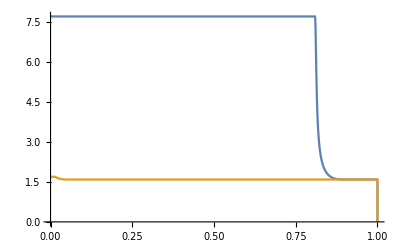

```mathematica
ListLinePlot[{drain,imbibe}, PlotRange->All]
```

This plot illustrates the hysteresis that is commonly cited in ink bottle examples. These results are driven by the geometry of the system, the direction of displacement, and the need to agree with Laplace’s equation at equilibrium.  These results assume an equilibrium state.

## Geometric State Equation

To evaluate the ink bottle in light of the geometric state equation, we need to evaluate the the Minkowski functionals for states within the system.  Since the geometric state equation applies under both equilibrium and non-equilibrium conditions, we could examine any set of states.  We also do not need the monotonicity condition that we applied to derive the ink-bottle example given above.  However, to make things simple, we will look at a similar set of states as examined above for consistency without loss of generality. 

The four Minkowski functionals of interest, in normalized form, are (1) M_0 or the volume fraction of the non-wetting phase; (2) M_1 the specific interfacial area of the non-wetting phase boundary; (3) M_2 the mean curvature of the non-wetting phase interface normalized by the volume; and (4) M_3 the specific Euler characteristic of the non-wetting phase. By inspection, we know that M_3 is constant for the ink-bottle example we have considered, since there is a only a single region of non-wetting phase away from the fully water saturated case and the connectivity of this region is a simple closed convex region without handles, etc.  This leaves three quantities to compute for a set of states in the system. We will define the functions needed in this section and provide a full analysis of the example in the section that follows.

First, let us consider M_0, which is the volume fraction of the non-wetting phase. We can derive this simply from our previous function to determine sw, which is also the volume fraction of the wetting phase for this case, since no solid is present.

```mathematica
M0[m_,n_,p_,q_,t_,xi_,xf_,xint_,xc_,r_]:=
1.-sw[m,n,p,q,t,xi,xf,xint,xc,r]
```

```mathematica
M0[0.01,.0.01,0.5,1.,0.75,0.,14.,14.,14.085799161736944,1.25813480653941]
```

0.113795

```mathematica
%+sw[0.01,.0.01,0.5,1.,0.75,0.,14.,14.,14.085799161736944,1.25813480653941]
```

1.

Now let us define the specific interfacial area of the non-wetting phase, which includes an ns component where the non-wetting fluid contacts the boundary of the ink bottle, and an nw component from the spherical cap of the meniscus interface. Because we have an axis of rotation, we need to integrate the radius of the ink bottle along the ns boundary to get this component. We will also need to compute a volume of the ink bottle in order to do our normalization.

```mathematica
V=volume[0.01,0.01,0.5,1.,0.75,0.,14.]
```

32.9077

```mathematica
areans[m_,n_,p_,q_,t_, xi_,xf_]:=Integrate[2 Pi y[m,n,p,q, t, x],{x,xi,xf}]
```

```mathematica
areawn[x_,xc_,r_]:=2 Pi r(r-(xc-x))
```

```mathematica
M1[m_,n_,p_,q_,t_,xi_,xf_,xint_,xc_,r_]:=
(areans[m,n,p,q,t,xint,xf] + areawn[xint,xc,r]
+ Pi y[m,n,p,q,t,xf]^2)/V
```

M2 is the mean curvature over the boundary of the non-wetting phase normalized by the volume of the domain. The principal directions of curvature in the ink bottle are the radius of curvature in the direction normal to x, which is the radius of the circular cross section, and the curvature in the x direction, which can be computed from a parametric form of the equation describing the geometry of the ink bottle. The curvature of spherical cap that describes the fluid-fluid interface is 2/r where r is the radius of the spherical cap. The integral of the mean ns curvature is computed by integrating over the ns interface. The integral of the wn curvature is just the area of the spherical wn cap times the mean curvature of the cap.

Let’s examine a parametric form of the equation. We can compute for example the arc length along the ink bottle, where we use s to denote that we are working in a parametric form.

```mathematica
ArcLength[{s,0.01 Cos [0.01 s]+0.5 Sin[ s] + 0.75},{s,0.,14.}]
```

14.8458

Use the built in function to compute the curvature along the ink bottle and define a function to compute this quantity for an arbitrary geometry of our general form. The ArcCurvature function returns the Frenet curvature (unsigned) of a parameteric curve. If we assume an orientation consistent with increasing x, we can deduce the sign of the curvature, which we will want for our application. This can be accomplished by examining the derivative of the slope of the ink bottle, or the second derivative of y.

```mathematica
D[m Cos [n x]+ p Sin[q x] + t,{x,2}]
```

-m n^2 Cos[n x]-p q^2 Sin[q x]

```mathematica
dydxx[m_,n_,p_,q_, x_]:= -m n^2 Cos[n x]-p q^2 Sin[q x]
```

```mathematica
dydxx[0.01,0.01,0.5,1.,0.9]
```

-0.391664

```mathematica
Length[stateSet]
```

142

```mathematica
dydxx[0.01,0.01,0.5,1.,stateSet[[1,4]]]
```

-1.×10^-6

```mathematica
Sign[dydxx[0.01,0.01,0.5,1.,stateSet[[1,4]]]]
```

-1

```mathematica
ArcCurvature[{s,m Cos [n s]+p Sin[q s] + t},s]
```

√(((m n^2 Cos[n s]+p q^2 Sin[q s])^2)/((1+p^2 q^2 Cos[q s]^2-2 m n p q Cos[q s] Sin[n s]+m^2 n^2 Sin[n s]^2)^3))

```mathematica
curvature[m_,n_,p_,q_,t_,s_]:= -Sign[dydxx[m,n,p,q,s]]√((m n^2 Cos[n s]+p q^2 Sin[q s])^2/(1+p^2 q^2 Cos[q s]^2-2 m n p q Cos[q s] Sin[n s]+m^2 n^2 Sin[n s]^2)^3)
```

```mathematica
curvature[0.01,0.01,0.5,1.,0.75,1.5707931853377164]
```

0.500001

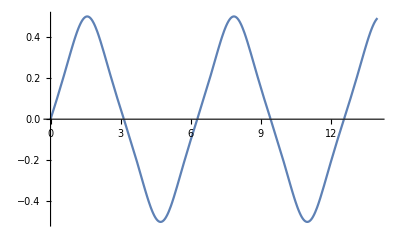

```mathematica
Plot[curvature[0.01,0.01,0.5,1.,0.75,s],{s,0.,14.}]
```

Now put the parts together to compute M2.

```mathematica
M2[m_,n_,p_,q_,t_,xi_,xf_,xint_,xc_,r_]:=
(NIntegrate[2.Pi y[m,n,p,q,t,x]((1./y[m,n,p,q,t, x])+curvature[m,n,p,q,t,x]),{x,xint,xf}]+(2. areawn[xint,xc,r]/r))/V
```

```mathematica
M2[0.01,0.01,0.5,1.,0.75,0.,14.,0.9,1.2579415794447057,1.2060057854786421]
```

3.15374

This provides the three normalized Minkowski functionals. of interest for the geometric state equation approach. Define a list for the M state in terms of xint, xc, r, M0, M1, and M2.

```mathematica
MstateSet=Table[0,{i,3,138},{j,1,6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Mlength=Length[MstateSet]
```

136

```mathematica
Do[MstateSet[[i,1]]=stateSet[[i+3,4]];MstateSet[[i,2]]=stateSet[[i+3,5]];MstateSet[[i,3]]=stateSet[[i+3,3]];MstateSet[[i,4]]=M0[0.01,0.01,0.5,1.,0.75,0.,14.,MstateSet[[i,1]],MstateSet[[i,2]],MstateSet[[i,3]]]; MstateSet[[i,5]]=M1[0.01,0.01,0.5,1.,0.75,0.,14.,MstateSet[[i,1]],MstateSet[[i,2]],MstateSet[[i,3]]]; MstateSet[[i,6]]=M2[0.01,0.01,0.5,1.,0.75,0.,14.,MstateSet[[i,1]],MstateSet[[i,2]],MstateSet[[i,3]]],{i,1,Mlength}]
```

```mathematica
MstateSet
```

{{0.9,1.25794,1.20601,0.981385,2.29283,3.15374},{1.,1.31898,1.22306,0.976919,2.2864,3.14802},{1.1,1.37343,1.23622,0.972396,2.27974,3.14231},{1.2,1.42213,1.24598,0.967814,2.27284,3.13657},{1.3,1.46609,1.25284,0.963144,2.26566,3.13073},{1.4,1.50646,1.25724,0.958323,2.25812,3.12468},{1.5,1.54452,1.25953,0.953239,2.25009,3.11828},{1.57079,1.57079,1.26,0.949397,2.24399,3.11344},{1.6,1.58161,1.25992,0.947735,2.24135,3.11135},{1.7,1.61909,1.25843,0.941599,2.23163,3.10362},{1.8,1.65835,1.25494,0.934579,2.22055,3.09478},{1.9,1.70067,1.24916,0.926392,2.2077,3.08444},{2.,1.74726,1.24066,0.916753,2.19262,3.07218},{2.1,1.79921,1.22898,0.905404,2.17484,3.05754},{2.2,1.85742,1.2136,0.892154,2.15397,3.04009},{2.3,1.9226,1.19406,0.876914,2.12971,3.01942},{2.4,1.99527,1.16996,0.859724,2.10191,2.99519},{2.5,2.0757,1.14105,0.840773,2.07058,2.96719},{2.6,2.16395,1.10723,0.820396,2.03597,2.93531},{2.7,2.25986,1.06855,0.799052,1.9985,2.89957},{2.8,2.36305,1.02526,0.777292,1.95879,2.86013},{2.9,2.47296,0.977801,0.755709,1.91757,2.81731},{3.,2.58888,0.926739,0.734879,1.87569,2.77151},{3.1,2.70994,0.872795,0.71532,1.83403,2.72326},{3.2,2.83522,0.816791,0.697441,1.79342,2.67317},{3.3,2.9637,0.759621,0.681524,1.75462,2.62189},{3.4,3.09438,0.702218,0.667711,1.71826,2.5701},{3.5,3.22627,0.645513,0.656015,1.68482,2.51847},{3.6,3.35844,0.59041,0.646337,1.65459,2.46765},{3.7,3.49006,0.537749,0.638496,1.6277,2.41821},{3.8,3.62042,0.488284,0.632261,1.60414,2.37068},{3.9,3.74896,0.442672,0.62738,1.58376,2.32548},{4.,3.87529,0.401454,0.6236,1.5663,2.28292},{4.1,3.99916,0.365057,0.620693,1.55145,2.24321},{4.2,4.12053,0.333802,0.618457,1.53888,2.20648},{4.3,4.2395,0.307911,0.616725,1.52823,2.17273},{4.4,4.35633,0.287525,0.615364,1.51917,2.14192},{4.5,4.47141,0.272727,0.614268,1.51138,2.11391},{4.6,4.58524,0.263557,0.613358,1.5046,2.08852},{4.7,4.69839,0.260032,0.612574,1.4986,2.06554},{4.7124,4.7124,0.259989,0.612483,1.4979,2.06285},{4.8,4.81146,0.262157,0.611868,1.49318,2.04475},{4.9,4.92506,0.269928,0.611204,1.4882,2.02592},{5.,5.03979,0.283333,0.610553,1.48352,2.00881},{5.1,5.15614,0.302338,0.609888,1.47905,1.99322},{5.2,5.27455,0.326875,0.609187,1.47471,1.97895},{5.3,5.39531,0.356817,0.608428,1.47047,1.96583},{5.4,5.51856,0.391964,0.607587,1.46627,1.9537},{5.5,5.64429,0.432022,0.606643,1.46209,1.94242},{5.6,5.77231,0.47659,0.605573,1.45792,1.93188},{5.7,5.90227,0.525155,0.604354,1.45375,1.92199},{5.8,6.03363,0.57709,0.602962,1.44956,1.91265},{5.9,6.16574,0.631662,0.601377,1.44534,1.90379},{6.,6.29778,0.688051,0.599576,1.44109,1.89537},{6.1,6.42885,0.745366,0.597541,1.43679,1.88733},{6.2,6.55797,0.802679,0.595256,1.43242,1.87963},{6.3,6.68413,0.859056,0.592711,1.42797,1.87225},{6.4,6.80633,0.91359,0.5899,1.42341,1.86513},{6.5,6.92361,0.965436,0.586822,1.41871,1.85828},{6.6,7.03508,1.01385,0.583485,1.41384,1.85164},{6.7,7.14,1.05821,0.579901,1.40878,1.84522},{6.8,7.23775,1.09806,0.576092,1.40351,1.83898},{6.9,7.32792,1.13311,0.572084,1.398,1.83289},{7.,7.41029,1.16323,0.56791,1.39225,1.82694},{7.1,7.48486,1.1885,0.563604,1.38625,1.8211},{7.2,7.55186,1.20914,0.559199,1.38002,1.81534},{7.3,7.61174,1.22551,0.554723,1.37355,1.80962},{7.4,7.66516,1.23806,0.55019,1.36685,1.80391},{7.5,7.71299,1.24729,0.545596,1.35991,1.79816},{7.6,7.75627,1.25371,0.540907,1.35267,1.79229},{7.7,7.79616,1.25774,0.53605,1.34506,1.78619},{7.8,7.83396,1.2597,0.530909,1.33693,1.77972},{7.85397,7.85397,1.25997,0.527958,1.33225,1.776},{7.9,7.87102,1.25977,0.525314,1.32805,1.77267},{8.,7.90871,1.25796,0.519048,1.31813,1.76478},{8.1,7.94839,1.25411,0.511852,1.30678,1.75571},{8.2,7.99135,1.2479,0.50344,1.29359,1.74508},{8.3,8.03878,1.2389,0.49353,1.27808,1.73245},{8.4,8.09172,1.22663,0.481873,1.25981,1.71737},{8.5,8.15106,1.21059,0.468292,1.23839,1.6994},{8.6,8.21748,1.1903,0.452718,1.21354,1.67815},{8.7,8.29144,1.16541,0.435215,1.18513,1.65331},{8.8,8.37319,1.13568,0.415998,1.15324,1.62466},{8.9,8.46274,1.10102,0.395423,1.11811,1.59212},{9.,8.55991,1.06154,0.37397,1.08022,1.55574},{9.1,8.66427,1.01752,0.3522,1.04019,1.51571},{9.2,8.77525,0.969409,0.330705,0.998804,1.47235},{9.3,8.8921,0.917808,0.310057,0.956904,1.4261},{9.4,9.01394,0.863457,0.290756,0.915362,1.3775},{9.5,9.13982,0.807191,0.273193,0.875008,1.32716},{9.6,9.26875,0.749916,0.257625,0.836581,1.27575},{9.7,9.3997,0.692565,0.244172,0.800687,1.22394},{9.8,9.5317,0.636068,0.232826,0.767768,1.1724},{9.9,9.66383,0.581318,0.223473,0.738097,1.12177},{10.,9.79529,0.529143,0.21592,0.711779,1.07262},{10.1,9.92538,0.480283,0.209932,0.688768,1.02546},{10.2,10.0536,0.435375,0.205254,0.668896,0.980677},{10.3,10.1795,0.39494,0.201637,0.651902,0.938582},{10.4,10.3029,0.359388,0.198857,0.637466,0.899371},{10.5,10.4239,0.329022,0.196717,0.625244,0.863141},{10.6,10.5425,0.304048,0.195057,0.614884,0.829898},{10.7,10.659,0.284597,0.193747,0.606056,0.799566},{10.8,10.7738,0.270743,0.192688,0.598458,0.772008},{10.9,10.8875,0.262521,0.191803,0.591827,0.74704},{10.9956,10.9956,0.25994,0.191067,0.586183,0.725396},{11.,11.0006,0.259945,0.191035,0.585937,0.724448},{11.1,11.1137,0.263019,0.190338,0.580604,0.704002},{11.2,11.2274,0.271737,0.189679,0.575677,0.685473},{11.3,11.3424,0.286086,0.189027,0.571039,0.668637},{11.4,11.4591,0.306027,0.188359,0.566597,0.653283},{11.5,11.5779,0.331481,0.18765,0.562284,0.639219},{11.6,11.699,0.362314,0.186878,0.558049,0.626273},{11.7,11.8227,0.398308,0.186022,0.553858,0.614294},{11.8,11.9488,0.439154,0.185059,0.549685,0.603149},{11.9,12.0772,0.484432,0.183966,0.545515,0.592726},{12.,12.2074,0.53361,0.182719,0.541337,0.582928},{12.1,12.339,0.58604,0.181297,0.537141,0.573675},{12.2,12.4711,0.640976,0.179677,0.53292,0.564899},{12.3,12.6031,0.697583,0.177838,0.528662,0.556544},{12.4,12.7339,0.754962,0.175762,0.524353,0.548565},{12.5,12.8626,0.812182,0.173435,0.519976,0.540921},{12.6,12.9881,0.868311,0.170846,0.515508,0.53358},{12.7,13.1096,0.922448,0.167991,0.510925,0.526513},{12.8,13.2259,0.973766,0.164869,0.506198,0.519694},{12.9,13.3364,1.02154,0.161489,0.5013,0.5131},{13.,13.4401,1.06517,0.157866,0.496206,0.506706},{13.1,13.5366,1.10423,0.154022,0.490892,0.500491},{13.2,13.6255,1.13844,0.149984,0.485343,0.49443},{13.3,13.7065,1.16774,0.145786,0.479552,0.4885},{13.4,13.7798,1.19221,0.141461,0.473516,0.482673},{13.5,13.8456,1.21211,0.137043,0.467242,0.476921},{13.6,13.9043,1.2278,0.132557,0.460735,0.47121},{13.7,13.9567,1.23976,0.128015,0.453996,0.465498},{13.8,14.0037,1.24849,0.123409,0.447006,0.45973},{13.9,14.0463,1.25447,0.118698,0.439716,0.453826},{14.,14.0858,1.25813,0.113803,0.43203,0.447676}}

Extract from this set a list for M0, M1 pairs for plotting and make the plot.

```mathematica
M0M1Set=Table[{MstateSet[[i,4]],MstateSet[[i,5]]},{i,1,Mlength}]
```

{{0.981385,2.29283},{0.976919,2.2864},{0.972396,2.27974},{0.967814,2.27284},{0.963144,2.26566},{0.958323,2.25812},{0.953239,2.25009},{0.949397,2.24399},{0.947735,2.24135},{0.941599,2.23163},{0.934579,2.22055},{0.926392,2.2077},{0.916753,2.19262},{0.905404,2.17484},{0.892154,2.15397},{0.876914,2.12971},{0.859724,2.10191},{0.840773,2.07058},{0.820396,2.03597},{0.799052,1.9985},{0.777292,1.95879},{0.755709,1.91757},{0.734879,1.87569},{0.71532,1.83403},{0.697441,1.79342},{0.681524,1.75462},{0.667711,1.71826},{0.656015,1.68482},{0.646337,1.65459},{0.638496,1.6277},{0.632261,1.60414},{0.62738,1.58376},{0.6236,1.5663},{0.620693,1.55145},{0.618457,1.53888},{0.616725,1.52823},{0.615364,1.51917},{0.614268,1.51138},{0.613358,1.5046},{0.612574,1.4986},{0.612483,1.4979},{0.611868,1.49318},{0.611204,1.4882},{0.610553,1.48352},{0.609888,1.47905},{0.609187,1.47471},{0.608428,1.47047},{0.607587,1.46627},{0.606643,1.46209},{0.605573,1.45792},{0.604354,1.45375},{0.602962,1.44956},{0.601377,1.44534},{0.599576,1.44109},{0.597541,1.43679},{0.595256,1.43242},{0.592711,1.42797},{0.5899,1.42341},{0.586822,1.41871},{0.583485,1.41384},{0.579901,1.40878},{0.576092,1.40351},{0.572084,1.398},{0.56791,1.39225},{0.563604,1.38625},{0.559199,1.38002},{0.554723,1.37355},{0.55019,1.36685},{0.545596,1.35991},{0.540907,1.35267},{0.53605,1.34506},{0.530909,1.33693},{0.527958,1.33225},{0.525314,1.32805},{0.519048,1.31813},{0.511852,1.30678},{0.50344,1.29359},{0.49353,1.27808},{0.481873,1.25981},{0.468292,1.23839},{0.452718,1.21354},{0.435215,1.18513},{0.415998,1.15324},{0.395423,1.11811},{0.37397,1.08022},{0.3522,1.04019},{0.330705,0.998804},{0.310057,0.956904},{0.290756,0.915362},{0.273193,0.875008},{0.257625,0.836581},{0.244172,0.800687},{0.232826,0.767768},{0.223473,0.738097},{0.21592,0.711779},{0.209932,0.688768},{0.205254,0.668896},{0.201637,0.651902},{0.198857,0.637466},{0.196717,0.625244},{0.195057,0.614884},{0.193747,0.606056},{0.192688,0.598458},{0.191803,0.591827},{0.191067,0.586183},{0.191035,0.585937},{0.190338,0.580604},{0.189679,0.575677},{0.189027,0.571039},{0.188359,0.566597},{0.18765,0.562284},{0.186878,0.558049},{0.186022,0.553858},{0.185059,0.549685},{0.183966,0.545515},{0.182719,0.541337},{0.181297,0.537141},{0.179677,0.53292},{0.177838,0.528662},{0.175762,0.524353},{0.173435,0.519976},{0.170846,0.515508},{0.167991,0.510925},{0.164869,0.506198},{0.161489,0.5013},{0.157866,0.496206},{0.154022,0.490892},{0.149984,0.485343},{0.145786,0.479552},{0.141461,0.473516},{0.137043,0.467242},{0.132557,0.460735},{0.128015,0.453996},{0.123409,0.447006},{0.118698,0.439716},{0.113803,0.43203}}

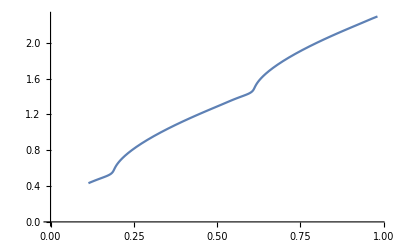

```mathematica
ListLinePlot[M0M1Set]
```

Extract from the set a list of M0,M2 pairs for plotting and make the plot.

```mathematica
M0M2Set=Table[{MstateSet[[i,4]],MstateSet[[i,6]]},{i,1,Mlength}]
```

{{0.981385,3.15374},{0.976919,3.14802},{0.972396,3.14231},{0.967814,3.13657},{0.963144,3.13073},{0.958323,3.12468},{0.953239,3.11828},{0.949397,3.11344},{0.947735,3.11135},{0.941599,3.10362},{0.934579,3.09478},{0.926392,3.08444},{0.916753,3.07218},{0.905404,3.05754},{0.892154,3.04009},{0.876914,3.01942},{0.859724,2.99519},{0.840773,2.96719},{0.820396,2.93531},{0.799052,2.89957},{0.777292,2.86013},{0.755709,2.81731},{0.734879,2.77151},{0.71532,2.72326},{0.697441,2.67317},{0.681524,2.62189},{0.667711,2.5701},{0.656015,2.51847},{0.646337,2.46765},{0.638496,2.41821},{0.632261,2.37068},{0.62738,2.32548},{0.6236,2.28292},{0.620693,2.24321},{0.618457,2.20648},{0.616725,2.17273},{0.615364,2.14192},{0.614268,2.11391},{0.613358,2.08852},{0.612574,2.06554},{0.612483,2.06285},{0.611868,2.04475},{0.611204,2.02592},{0.610553,2.00881},{0.609888,1.99322},{0.609187,1.97895},{0.608428,1.96583},{0.607587,1.9537},{0.606643,1.94242},{0.605573,1.93188},{0.604354,1.92199},{0.602962,1.91265},{0.601377,1.90379},{0.599576,1.89537},{0.597541,1.88733},{0.595256,1.87963},{0.592711,1.87225},{0.5899,1.86513},{0.586822,1.85828},{0.583485,1.85164},{0.579901,1.84522},{0.576092,1.83898},{0.572084,1.83289},{0.56791,1.82694},{0.563604,1.8211},{0.559199,1.81534},{0.554723,1.80962},{0.55019,1.80391},{0.545596,1.79816},{0.540907,1.79229},{0.53605,1.78619},{0.530909,1.77972},{0.527958,1.776},{0.525314,1.77267},{0.519048,1.76478},{0.511852,1.75571},{0.50344,1.74508},{0.49353,1.73245},{0.481873,1.71737},{0.468292,1.6994},{0.452718,1.67815},{0.435215,1.65331},{0.415998,1.62466},{0.395423,1.59212},{0.37397,1.55574},{0.3522,1.51571},{0.330705,1.47235},{0.310057,1.4261},{0.290756,1.3775},{0.273193,1.32716},{0.257625,1.27575},{0.244172,1.22394},{0.232826,1.1724},{0.223473,1.12177},{0.21592,1.07262},{0.209932,1.02546},{0.205254,0.980677},{0.201637,0.938582},{0.198857,0.899371},{0.196717,0.863141},{0.195057,0.829898},{0.193747,0.799566},{0.192688,0.772008},{0.191803,0.74704},{0.191067,0.725396},{0.191035,0.724448},{0.190338,0.704002},{0.189679,0.685473},{0.189027,0.668637},{0.188359,0.653283},{0.18765,0.639219},{0.186878,0.626273},{0.186022,0.614294},{0.185059,0.603149},{0.183966,0.592726},{0.182719,0.582928},{0.181297,0.573675},{0.179677,0.564899},{0.177838,0.556544},{0.175762,0.548565},{0.173435,0.540921},{0.170846,0.53358},{0.167991,0.526513},{0.164869,0.519694},{0.161489,0.5131},{0.157866,0.506706},{0.154022,0.500491},{0.149984,0.49443},{0.145786,0.4885},{0.141461,0.482673},{0.137043,0.476921},{0.132557,0.47121},{0.128015,0.465498},{0.123409,0.45973},{0.118698,0.453826},{0.113803,0.447676}}

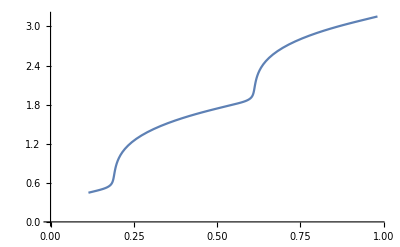

```mathematica
ListLinePlot[M0M2Set]
```

Note that the above plot is the total normalized mean curvature of the boundary of the non-wetting phase.  The end-points have been ignored to focus on equilibrium states within the domain that involve two fluid phases.   This profile is monotonic an invertible.  Thus, these results look like the ones we obtained before for the Physical Review Fluids paper.